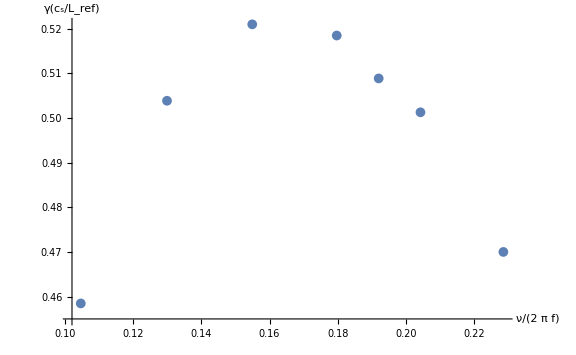

```mathematica
Data=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\DIIID\\conference\\nu_ei\\nu_ei.xlsx"];
Show[
ListPlot[Data,
AxesLabel->{Style[ToExpression["\\frac{\\nu}{2 \\pi f}",TeXForm,HoldForm
]
,Bold,20],
Style[ToExpression["\\gamma(\\frac{c_s}{L_{ref}})",TeXForm,HoldForm
]
,Bold,20]},
PlotMarkers->{Automatic,Medium},
AxesStyle->Directive[Black,20]
],
ImageSize->Large,
(*PlotLabel->"Local Linear GENE Simluation at x/a=0.98",*)
BaseStyle->{FontSize->15}
]
```

```mathematica
Plot[2 Sin[x],{x,0,10},AxesLabel->{x,2 Sin[x]},LabelStyle->Directive[Blue,Bold]]
```